```mathematica
focus={a,b}; 
(* Point in R^2*)
directrix={x,c x+d}; 
(* Equation of form y = c x + b *)
```

```mathematica
distfromf=Norm[{x,y}-focus];
distfromd=Norm[{x,y}-directrix];
genform=Solve[distfromd==distfromf,y]//Quiet;
```

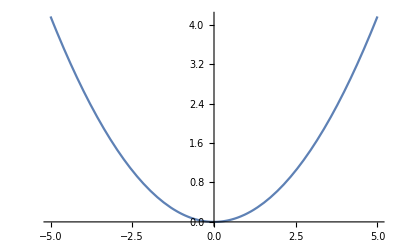

√(Abs[-1+x]^2+Abs[-1+y]^2)

```mathematica
Plot[y/.(genform/.{a->0,b->1.5,c->0,d->-1.5}),{x,-5,5}]
```